```mathematica
PRatioHuge[tuple_]:=PRatioHuge[tuple]=PRatio[Sort[tuple], Sort[tuple], 100000000]
```

```mathematica
PRatio[{3,5},{3,5}, 10]
```

3/10

```mathematica
PRatio[{3,5},{3,5}, 100]
```

13/100

```mathematica
PRatio[{3,5},{3,5}, 1000]
```

19/500

```mathematica
PRatio[{3,5},{3,5}, 10000]
```

23/2000

```mathematica
PRatio[{3,5},{3,5}, 100000]
```

159/50000

```mathematica
PRatio[{3,5},{3,5}, 1000000000]
```

921/40000000

```mathematica
PRatio[{3,5},{3,5}, 1000000]
```

193/250000

```mathematica
PRatio[{3,5},{3,5}, 10000000]
```

1811/10000000

```mathematica
N[193/250000]
```

0.000772

```mathematica
N[1811/10000000]
```

0.0001811

```mathematica
N[921/40000000]
```

0.000023025

```mathematica
N[Log[3*5*7*11,20000000]]
```

2.38395

```mathematica
Clear[PRatioHuge]
```

```mathematica
couples= Flatten[
{Subsets[Prime[Range[2,4]],{2}],
Subsets[Prime[Range[10,11]],{2}],
Subsets[Prime[Range[25,26]],{2}]
}, 1
]
```

{{3,5},{3,7},{5,7}}

```mathematica
ListPlot[
Sort[
Table[
Tooltip[{N[magicGraham[tuple]], PRatioHuge[tuple]}, tuple],
{tuple,
couples}
]
],
PlotMarkers->Automatic,
GridLines->Automatic,
Frame->True,
PlotLabel->"Ratio {p,q}-good in union {p-good, q-good} with size 10.000.000"
]
```

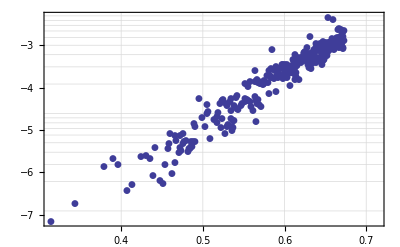

```mathematica
ListLogPlot[
Sort[
Table[
Tooltip[{N[magicGraham[tuple]], PRatioHuge[tuple]}, tuple],
{tuple, Subsets[Prime[Range[2,31]],{2,2}]}
]
],
PlotMarkers->Automatic,
GridLines->Automatic,
Frame->True,
PlotLabel->"Ratio {p,q}-good in union {p-good, q-good} with size 20.000.000"
]
```

```mathematica
ListPlot3D[
Flatten[
Table[{Append[tuple,PRatioHuge[tuple]], Append[Reverse[tuple],PRatioHuge[tuple]]},{tuple,Subsets[Prime[Range[2,35]],{2}]}],
1],
ColorFunction->"DarkRainbow",
ImageSize->800
]
```

```mathematica
Clear[PRatioHuge]
```

```mathematica
Sort[
Table[
{tuple, PRatioHuge[tuple]},
{tuple, Subsets[Prime[Range[2,30]],{2}]}
]
]
```

{{{3,5},193/250000},{{3,7},593/500000},{{3,11},2837/1000000},{{3,13},3449/1000000},{{3,17},407/250000},{{3,19},29/15625},{{3,23},3649/1000000},{{3,29},1737/500000},{{3,31},2319/1000000},{{3,37},207/100000},{{3,41},477/250000},{{3,43},119/40000},{{3,47},547/125000},{{3,53},481/200000},{{3,59},157/50000},{{3,61},1329/250000},{{3,67},397/100000},{{3,71},2213/500000},{{3,73},523/125000},{{3,79},4859/1000000},{{3,83},5091/1000000},{{3,89},82/15625},{{3,97},1019/250000},{{3,101},4381/1000000},{{3,103},2181/500000},{{3,107},1023/200000},{{3,109},4579/1000000},{{3,113},2281/500000},{{5,7},3001/1000000},{{5,11},3723/1000000},{{5,13},4459/1000000},{{5,17},4929/1000000},{{5,19},5867/1000000},{{5,23},6179/1000000},{{5,29},1037/200000},{{5,31},7393/1000000},{{5,37},4489/500000},{{5,41},3697/500000},{{5,43},987/100000},{{5,47},1383/250000},{{5,53},2177/250000},{{5,59},9321/1000000},{{5,61},10181/1000000},{{5,67},7247/1000000},{{5,71},2217/250000},{{5,73},6961/500000},{{5,79},6177/1000000},{{5,83},7349/1000000},{{5,89},477/62500},{{5,97},4443/500000},{{5,101},6753/1000000},{{5,103},1837/250000},{{5,107},721/100000},{{5,109},523/62500},{{5,113},4203/500000},{{7,11},77/12500},{{7,13},5929/1000000},{{7,17},3919/500000},{{7,19},3521/250000},{{7,23},12339/1000000},{{7,29},8037/1000000},{{7,31},6259/500000},{{7,37},3129/250000},{{7,41},6589/500000},{{7,43},10639/1000000},{{7,47},11959/1000000},{{7,53},10993/1000000},{{7,59},3011/250000},{{7,61},6341/500000},{{7,67},1327/100000},{{7,71},429/31250},{{7,73},3361/250000},{{7,79},6603/500000},{{7,83},2943/250000},{{7,89},1067/100000},{{7,97},1481/100000},{{7,101},8313/1000000},{{7,103},6727/500000},{{7,107},3173/250000},{{7,109},697/50000},{{7,113},12427/1000000},{{11,13},10353/1000000},{{11,17},13629/1000000},{{11,19},2433/200000},{{11,23},1463/100000},{{11,29},318/15625},{{11,31},4727/250000},{{11,37},27709/1000000},{{11,41},10317/500000},{{11,43},1259/62500},{{11,47},3943/200000},{{11,53},24673/1000000},{{11,59},12179/500000},{{11,61},23163/1000000},{{11,67},11417/500000},{{11,71},109/4000},{{11,73},4823/200000},{{11,79},4719/200000},{{11,83},12543/500000},{{11,89},24183/1000000},{{11,97},22729/1000000},{{11,101},24209/1000000},{{11,103},26073/1000000},{{11,107},1271/50000},{{11,109},6811/250000},{{11,113},5989/250000},{{13,17},14213/1000000},{{13,19},15153/1000000},{{13,23},14173/1000000},{{13,29},21027/1000000},{{13,31},22227/1000000},{{13,37},2151/100000},{{13,41},10409/500000},{{13,43},3231/200000},{{13,47},45577/1000000},{{13,53},16883/1000000},{{13,59},3059/125000},{{13,61},4789/200000},{{13,67},24609/1000000},{{13,71},2537/100000},{{13,73},13939/500000},{{13,79},5867/250000},{{13,83},26021/1000000},{{13,89},26219/1000000},{{13,97},1633/62500},{{13,101},25839/1000000},{{13,103},30167/1000000},{{13,107},22057/1000000},{{13,109},1209/50000},{{13,113},817/31250},{{17,19},21151/1000000},{{17,23},10617/500000},{{17,29},13881/500000},{{17,31},28853/1000000},{{17,37},1123/40000},{{17,41},1797/62500},{{17,43},30853/1000000},{{17,47},1039/40000},{{17,53},3333/125000},{{17,59},8867/250000},{{17,61},16957/500000},{{17,67},35359/1000000},{{17,71},16541/500000},{{17,73},8501/250000},{{17,79},33061/1000000},{{17,83},34701/1000000},{{17,89},17679/500000},{{17,97},35983/1000000},{{17,101},683/20000},{{17,103},9001/250000},{{17,107},14721/500000},{{17,109},8027/200000},{{17,113},60833/1000000},{{19,23},253/12500},{{19,29},5687/200000},{{19,31},30253/1000000},{{19,37},31417/1000000},{{19,41},32089/1000000},{{19,43},29357/1000000},{{19,47},27837/1000000},{{19,53},17967/500000},{{19,59},37517/1000000},{{19,61},36717/1000000},{{19,67},149/4000},{{19,71},1203/31250},{{19,73},41911/1000000},{{19,79},4079/100000},{{19,83},6953/200000},{{19,89},37101/1000000},{{19,97},37127/1000000},{{19,101},18379/500000},{{19,103},4291/125000},{{19,107},39879/1000000},{{19,109},34467/1000000},{{19,113},33501/1000000},{{23,29},3189/100000},{{23,31},31639/1000000},{{23,37},30957/1000000},{{23,41},14853/500000},{{23,43},31331/1000000},{{23,47},34647/1000000},{{23,53},41451/1000000},{{23,59},33889/1000000},{{23,61},7871/250000},{{23,67},5749/200000},{{23,71},809/25000},{{23,73},6947/200000},{{23,79},6823/200000},{{23,83},2191/62500},{{23,89},1077/31250},{{23,97},7069/200000},{{23,101},7073/200000},{{23,103},31489/1000000},{{23,107},35097/1000000},{{23,109},38363/1000000},{{23,113},36541/1000000},{{29,31},40357/1000000},{{29,37},2347/62500},{{29,41},21683/500000},{{29,43},39223/1000000},{{29,47},41589/1000000},{{29,53},8177/200000},{{29,59},12933/250000},{{29,61},24913/500000},{{29,67},12323/250000},{{29,71},9671/200000},{{29,73},47851/1000000},{{29,79},1611/31250},{{29,83},45499/1000000},{{29,89},48087/500000},{{29,97},193/4000},{{29,101},12969/250000},{{29,103},50717/1000000},{{29,107},49713/1000000},{{29,109},49987/1000000},{{29,113},50517/1000000},{{31,37},19339/500000},{{31,41},9423/200000},{{31,43},4639/125000},{{31,47},42597/1000000},{{31,53},23957/500000},{{31,59},10191/200000},{{31,61},51731/1000000},{{31,67},27553/500000},{{31,71},52441/1000000},{{31,73},12463/250000},{{31,79},6291/125000},{{31,83},52739/1000000},{{31,89},47833/1000000},{{31,97},45771/500000},{{31,101},23307/500000},{{31,103},9123/200000},{{31,107},55323/1000000},{{31,109},50171/1000000},{{31,113},12651/250000},{{37,41},22713/500000},{{37,43},2199/62500},{{37,47},11083/250000},{{37,53},8609/200000},{{37,59},53507/1000000},{{37,61},26139/500000},{{37,67},1049/20000},{{37,71},25697/500000},{{37,73},51917/1000000},{{37,79},3313/62500},{{37,83},1597/31250},{{37,89},12599/250000},{{37,97},10697/200000},{{37,101},55237/1000000},{{37,103},53539/1000000},{{37,107},53591/1000000},{{37,109},14299/250000},{{37,113},11969/250000},{{41,43},47379/1000000},{{41,47},10307/250000},{{41,53},48579/1000000},{{41,59},26827/500000},{{41,61},25829/500000},{{41,67},6449/125000},{{41,71},14131/250000},{{41,73},13051/250000},{{41,79},26813/500000},{{41,83},29859/500000},{{41,89},51043/1000000},{{41,97},30899/500000},{{41,101},56257/1000000},{{41,103},49799/1000000},{{41,107},29493/500000},{{41,109},27519/500000},{{41,113},25681/500000},{{43,47},36079/1000000},{{43,53},43047/1000000},{{43,59},54947/1000000},{{43,61},58253/1000000},{{43,67},55593/1000000},{{43,71},13487/250000},{{43,73},60721/1000000},{{43,79},60193/1000000},{{43,83},10977/200000},{{43,89},61807/1000000},{{43,97},1681/31250},{{43,101},7941/125000},{{43,103},65307/1000000},{{43,107},15427/250000},{{43,109},59611/1000000},{{43,113},54423/1000000},{{47,53},5707/125000},{{47,59},23181/500000},{{47,61},5999/125000},{{47,67},48351/1000000},{{47,71},2989/62500},{{47,73},9609/200000},{{47,79},24363/500000},{{47,83},5801/125000},{{47,89},13493/250000},{{47,97},51157/1000000},{{47,101},24869/500000},{{47,103},51009/1000000},{{47,107},25707/500000},{{47,109},22271/500000},{{47,113},52669/1000000},{{53,59},2909/40000},{{53,61},18597/250000},{{53,67},35827/500000},{{53,71},69719/1000000},{{53,73},34993/500000},{{53,79},17229/250000},{{53,83},68553/1000000},{{53,89},7421/100000},{{53,97},7321/100000},{{53,101},74777/1000000},{{53,103},76003/1000000},{{53,107},78473/1000000},{{53,109},70147/1000000},{{53,113},74063/1000000},{{59,61},66717/1000000},{{59,67},2277/31250},{{59,71},73081/1000000},{{59,73},14891/200000},{{59,79},35979/500000},{{59,83},70439/1000000},{{59,89},72521/1000000},{{59,97},36753/500000},{{59,101},20813/250000},{{59,103},40153/500000},{{59,107},14209/200000},{{59,109},36423/500000},{{59,113},41291/500000},{{61,67},73493/1000000},{{61,71},71339/1000000},{{61,73},74563/1000000},{{61,79},1106/15625},{{61,83},4361/62500},{{61,89},34443/500000},{{61,97},187/2500},{{61,101},8657/125000},{{61,103},35857/500000},{{61,107},75179/1000000},{{61,109},72511/1000000},{{61,113},1151/15625},{{67,71},15069/200000},{{67,73},71947/1000000},{{67,79},72913/1000000},{{67,83},70879/1000000},{{67,89},9063/125000},{{67,97},21939/250000},{{67,101},17379/250000},{{67,103},38199/500000},{{67,107},73413/1000000},{{67,109},74557/1000000},{{67,113},72477/1000000},{{71,73},12411/200000},{{71,79},73229/1000000},{{71,83},71287/1000000},{{71,89},18013/250000},{{71,97},35767/500000},{{71,101},72793/1000000},{{71,103},88049/1000000},{{71,107},3719/50000},{{71,109},71587/1000000},{{71,113},9347/125000},{{73,79},1188/15625},{{73,83},36749/500000},{{73,89},1431/20000},{{73,97},7277/100000},{{73,101},73041/1000000},{{73,103},71199/1000000},{{73,107},71473/1000000},{{73,109},1487/20000},{{73,113},74169/1000000},{{79,83},9743/125000},{{79,89},9179/125000},{{79,97},69167/1000000},{{79,101},72953/1000000},{{79,103},15301/200000},{{79,107},34187/500000},{{79,109},18489/250000},{{79,113},87117/1000000},{{83,89},78481/1000000},{{83,97},17399/250000},{{83,101},36769/500000},{{83,103},1507/20000},{{83,107},68089/1000000},{{83,109},6997/100000},{{83,113},19367/250000},{{89,97},20663/250000},{{89,101},1697/25000},{{89,103},9437/125000},{{89,107},78329/1000000},{{89,109},70371/1000000},{{89,113},9259/125000},{{97,101},18553/250000},{{97,103},12811/200000},{{97,107},9777/125000},{{97,109},16029/200000},{{97,113},36371/500000},{{101,103},67847/1000000},{{101,107},31141/500000},{{101,109},62057/1000000},{{101,113},3271/40000},{{103,107},91417/1000000},{{103,109},66151/1000000},{{103,113},8781/125000},{{107,109},64817/1000000},{{107,113},15067/200000},{{109,113},49309/500000}}

```mathematica
N[magicGraham[{97,101}]  ]
```

0.702669

```mathematica
Subsets[Prime[Range[2,8]],{2}]
```

{{3,5},{3,7},{3,11},{3,13},{3,17},{3,19},{5,7},{5,11},{5,13},{5,17},{5,19},{7,11},{7,13},{7,17},{7,19},{11,13},{11,17},{11,19},{13,17},{13,19},{17,19}}

```mathematica
N[1181177/20000000]
```

```mathematica
1/Exp[0.05905885]
```

0.942651

```mathematica
ListPlot3D[
Inverse[
Table[
If[p==q,0,PRatioHuge[Sort[{p,q}]]], {p, Prime[Range[2,21]]}, {q, Prime[Range[2,20]]}
]
],
ColorFunction->"DarkRainbow",
ImageSize->800
]
```

Inverse::matsq: Argument {{0, 193/250000, 593/500000, 2837/1000000, 3449/1000000, 407/250000, 29/15625, 3649/1000000, 1737/500000, 2319/1000000, « 9 »}, {193/250000, 0, 3001/1000000, 3723/1000000, 4459/1000000, 4929/1000000, 5867/1000000, 6179/1000000, 1037/200000, 7393/1000000, « 9 »}, « 8 », « 10 »} at position 1 is not a non-empty square matrix.

ListPlot3D::arrayerr: Inverse[{{0, 193/250000, 593/500000, 2837/1000000, 3449/1000000, 407/250000, 29/15625, 3649/1000000, 1737/500000, 2319/1000000, « 9 »}, {193/250000, 0, 3001/1000000, 3723/1000000, 4459/1000000, 4929/1000000, 5867/1000000, 6179/1000000, 1037/200000, 7393/1000000, « 9 »}, « 8 », « 10 »}] must be a valid array or a list of valid arrays.

```mathematica
ListPlot3D[m,ColorFunction->"DarkRainbow",ImageSize->800]
```

-Graphics3D-

```mathematica
ListPlot3D[Inverse[m],ColorFunction->"DarkRainbow",ImageSize->800]
```

-Graphics3D-

```mathematica
m=Table[
If[p==q,0,PRatioHuge[Sort[{p,q}]]], {p, Prime[Range[2,31]]}, {q, Prime[Range[2,31]]}
]
```

{{0,193/250000,593/500000,2837/1000000,3449/1000000,407/250000,29/15625,3649/1000000,1737/500000,2319/1000000,207/100000,477/250000,119/40000,547/125000,481/200000,157/50000,1329/250000,397/100000,2213/500000,523/125000,4859/1000000,5091/1000000,82/15625,1019/250000,4381/1000000,2181/500000,1023/200000,4579/1000000,2281/500000,5193/1000000},{193/250000,0,3001/1000000,3723/1000000,4459/1000000,4929/1000000,5867/1000000,6179/1000000,1037/200000,7393/1000000,4489/500000,3697/500000,987/100000,1383/250000,2177/250000,9321/1000000,10181/1000000,7247/1000000,2217/250000,6961/500000,6177/1000000,7349/1000000,477/62500,4443/500000,6753/1000000,1837/250000,721/100000,523/62500,4203/500000,11341/1000000},{593/500000,3001/1000000,0,77/12500,5929/1000000,3919/500000,3521/250000,12339/1000000,8037/1000000,6259/500000,3129/250000,6589/500000,10639/1000000,11959/1000000,10993/1000000,3011/250000,6341/500000,1327/100000,429/31250,3361/250000,6603/500000,2943/250000,1067/100000,1481/100000,8313/1000000,6727/500000,3173/250000,697/50000,12427/1000000,11807/1000000},{2837/1000000,3723/1000000,77/12500,0,10353/1000000,13629/1000000,2433/200000,1463/100000,318/15625,4727/250000,27709/1000000,10317/500000,1259/62500,3943/200000,24673/1000000,12179/500000,23163/1000000,11417/500000,109/4000,4823/200000,4719/200000,12543/500000,24183/1000000,22729/1000000,24209/1000000,26073/1000000,1271/50000,6811/250000,5989/250000,243/12500},{3449/1000000,4459/1000000,5929/1000000,10353/1000000,0,14213/1000000,15153/1000000,14173/1000000,21027/1000000,22227/1000000,2151/100000,10409/500000,3231/200000,45577/1000000,16883/1000000,3059/125000,4789/200000,24609/1000000,2537/100000,13939/500000,5867/250000,26021/1000000,26219/1000000,1633/62500,25839/1000000,30167/1000000,22057/1000000,1209/50000,817/31250,22151/1000000},{407/250000,4929/1000000,3919/500000,13629/1000000,14213/1000000,0,21151/1000000,10617/500000,13881/500000,28853/1000000,1123/40000,1797/62500,30853/1000000,1039/40000,3333/125000,8867/250000,16957/500000,35359/1000000,16541/500000,8501/250000,33061/1000000,34701/1000000,17679/500000,35983/1000000,683/20000,9001/250000,14721/500000,8027/200000,60833/1000000,36117/1000000},{29/15625,5867/1000000,3521/250000,2433/200000,15153/1000000,21151/1000000,0,253/12500,5687/200000,30253/1000000,31417/1000000,32089/1000000,29357/1000000,27837/1000000,17967/500000,37517/1000000,36717/1000000,149/4000,1203/31250,41911/1000000,4079/100000,6953/200000,37101/1000000,37127/1000000,18379/500000,4291/125000,39879/1000000,34467/1000000,33501/1000000,37397/1000000},{3649/1000000,6179/1000000,12339/1000000,1463/100000,14173/1000000,10617/500000,253/12500,0,3189/100000,31639/1000000,30957/1000000,14853/500000,31331/1000000,34647/1000000,41451/1000000,33889/1000000,7871/250000,5749/200000,809/25000,6947/200000,6823/200000,2191/62500,1077/31250,7069/200000,7073/200000,31489/1000000,35097/1000000,38363/1000000,36541/1000000,19439/500000},{1737/500000,1037/200000,8037/1000000,318/15625,21027/1000000,13881/500000,5687/200000,3189/100000,0,40357/1000000,2347/62500,21683/500000,39223/1000000,41589/1000000,8177/200000,12933/250000,24913/500000,12323/250000,9671/200000,47851/1000000,1611/31250,45499/1000000,48087/500000,193/4000,12969/250000,50717/1000000,49713/1000000,49987/1000000,50517/1000000,58581/1000000},{2319/1000000,7393/1000000,6259/500000,4727/250000,22227/1000000,28853/1000000,30253/1000000,31639/1000000,40357/1000000,0,19339/500000,9423/200000,4639/125000,42597/1000000,23957/500000,10191/200000,51731/1000000,27553/500000,52441/1000000,12463/250000,6291/125000,52739/1000000,47833/1000000,45771/500000,23307/500000,9123/200000,55323/1000000,50171/1000000,12651/250000,24689/500000},{207/100000,4489/500000,3129/250000,27709/1000000,2151/100000,1123/40000,31417/1000000,30957/1000000,2347/62500,19339/500000,0,22713/500000,2199/62500,11083/250000,8609/200000,53507/1000000,26139/500000,1049/20000,25697/500000,51917/1000000,3313/62500,1597/31250,12599/250000,10697/200000,55237/1000000,53539/1000000,53591/1000000,14299/250000,11969/250000,7997/100000},{477/250000,3697/500000,6589/500000,10317/500000,10409/500000,1797/62500,32089/1000000,14853/500000,21683/500000,9423/200000,22713/500000,0,47379/1000000,10307/250000,48579/1000000,26827/500000,25829/500000,6449/125000,14131/250000,13051/250000,26813/500000,29859/500000,51043/1000000,30899/500000,56257/1000000,49799/1000000,29493/500000,27519/500000,25681/500000,25043/500000},{119/40000,987/100000,10639/1000000,1259/62500,3231/200000,30853/1000000,29357/1000000,31331/1000000,39223/1000000,4639/125000,2199/62500,47379/1000000,0,36079/1000000,43047/1000000,54947/1000000,58253/1000000,55593/1000000,13487/250000,60721/1000000,60193/1000000,10977/200000,61807/1000000,1681/31250,7941/125000,65307/1000000,15427/250000,59611/1000000,54423/1000000,13233/250000},{547/125000,1383/250000,11959/1000000,3943/200000,45577/1000000,1039/40000,27837/1000000,34647/1000000,41589/1000000,42597/1000000,11083/250000,10307/250000,36079/1000000,0,5707/125000,23181/500000,5999/125000,48351/1000000,2989/62500,9609/200000,24363/500000,5801/125000,13493/250000,51157/1000000,24869/500000,51009/1000000,25707/500000,22271/500000,52669/1000000,12363/250000},{481/200000,2177/250000,10993/1000000,24673/1000000,16883/1000000,3333/125000,17967/500000,41451/1000000,8177/200000,23957/500000,8609/200000,48579/1000000,43047/1000000,5707/125000,0,2909/40000,18597/250000,35827/500000,69719/1000000,34993/500000,17229/250000,68553/1000000,7421/100000,7321/100000,74777/1000000,76003/1000000,78473/1000000,70147/1000000,74063/1000000,34773/500000},{157/50000,9321/1000000,3011/250000,12179/500000,3059/125000,8867/250000,37517/1000000,33889/1000000,12933/250000,10191/200000,53507/1000000,26827/500000,54947/1000000,23181/500000,2909/40000,0,66717/1000000,2277/31250,73081/1000000,14891/200000,35979/500000,70439/1000000,72521/1000000,36753/500000,20813/250000,40153/500000,14209/200000,36423/500000,41291/500000,1727/25000},{1329/250000,10181/1000000,6341/500000,23163/1000000,4789/200000,16957/500000,36717/1000000,7871/250000,24913/500000,51731/1000000,26139/500000,25829/500000,58253/1000000,5999/125000,18597/250000,66717/1000000,0,73493/1000000,71339/1000000,74563/1000000,1106/15625,4361/62500,34443/500000,187/2500,8657/125000,35857/500000,75179/1000000,72511/1000000,1151/15625,77633/1000000},{397/100000,7247/1000000,1327/100000,11417/500000,24609/1000000,35359/1000000,149/4000,5749/200000,12323/250000,27553/500000,1049/20000,6449/125000,55593/1000000,48351/1000000,35827/500000,2277/31250,73493/1000000,0,15069/200000,71947/1000000,72913/1000000,70879/1000000,9063/125000,21939/250000,17379/250000,38199/500000,73413/1000000,74557/1000000,72477/1000000,36217/500000},{2213/500000,2217/250000,429/31250,109/4000,2537/100000,16541/500000,1203/31250,809/25000,9671/200000,52441/1000000,25697/500000,14131/250000,13487/250000,2989/62500,69719/1000000,73081/1000000,71339/1000000,15069/200000,0,12411/200000,73229/1000000,71287/1000000,18013/250000,35767/500000,72793/1000000,88049/1000000,3719/50000,71587/1000000,9347/125000,35987/500000},{523/125000,6961/500000,3361/250000,4823/200000,13939/500000,8501/250000,41911/1000000,6947/200000,47851/1000000,12463/250000,51917/1000000,13051/250000,60721/1000000,9609/200000,34993/500000,14891/200000,74563/1000000,71947/1000000,12411/200000,0,1188/15625,36749/500000,1431/20000,7277/100000,73041/1000000,71199/1000000,71473/1000000,1487/20000,74169/1000000,35001/500000},{4859/1000000,6177/1000000,6603/500000,4719/200000,5867/250000,33061/1000000,4079/100000,6823/200000,1611/31250,6291/125000,3313/62500,26813/500000,60193/1000000,24363/500000,17229/250000,35979/500000,1106/15625,72913/1000000,73229/1000000,1188/15625,0,9743/125000,9179/125000,69167/1000000,72953/1000000,15301/200000,34187/500000,18489/250000,87117/1000000,71377/1000000},{5091/1000000,7349/1000000,2943/250000,12543/500000,26021/1000000,34701/1000000,6953/200000,2191/62500,45499/1000000,52739/1000000,1597/31250,29859/500000,10977/200000,5801/125000,68553/1000000,70439/1000000,4361/62500,70879/1000000,71287/1000000,36749/500000,9743/125000,0,78481/1000000,17399/250000,36769/500000,1507/20000,68089/1000000,6997/100000,19367/250000,17843/250000},{82/15625,477/62500,1067/100000,24183/1000000,26219/1000000,17679/500000,37101/1000000,1077/31250,48087/500000,47833/1000000,12599/250000,51043/1000000,61807/1000000,13493/250000,7421/100000,72521/1000000,34443/500000,9063/125000,18013/250000,1431/20000,9179/125000,78481/1000000,0,20663/250000,1697/25000,9437/125000,78329/1000000,70371/1000000,9259/125000,83801/1000000},{1019/250000,4443/500000,1481/100000,22729/1000000,1633/62500,35983/1000000,37127/1000000,7069/200000,193/4000,45771/500000,10697/200000,30899/500000,1681/31250,51157/1000000,7321/100000,36753/500000,187/2500,21939/250000,35767/500000,7277/100000,69167/1000000,17399/250000,20663/250000,0,18553/250000,12811/200000,9777/125000,16029/200000,36371/500000,37871/500000},{4381/1000000,6753/1000000,8313/1000000,24209/1000000,25839/1000000,683/20000,18379/500000,7073/200000,12969/250000,23307/500000,55237/1000000,56257/1000000,7941/125000,24869/500000,74777/1000000,20813/250000,8657/125000,17379/250000,72793/1000000,73041/1000000,72953/1000000,36769/500000,1697/25000,18553/250000,0,67847/1000000,31141/500000,62057/1000000,3271/40000,66903/1000000},{2181/500000,1837/250000,6727/500000,26073/1000000,30167/1000000,9001/250000,4291/125000,31489/1000000,50717/1000000,9123/200000,53539/1000000,49799/1000000,65307/1000000,51009/1000000,76003/1000000,40153/500000,35857/500000,38199/500000,88049/1000000,71199/1000000,15301/200000,1507/20000,9437/125000,12811/200000,67847/1000000,0,91417/1000000,66151/1000000,8781/125000,8929/125000},{1023/200000,721/100000,3173/250000,1271/50000,22057/1000000,14721/500000,39879/1000000,35097/1000000,49713/1000000,55323/1000000,53591/1000000,29493/500000,15427/250000,25707/500000,78473/1000000,14209/200000,75179/1000000,73413/1000000,3719/50000,71473/1000000,34187/500000,68089/1000000,78329/1000000,9777/125000,31141/500000,91417/1000000,0,64817/1000000,15067/200000,15889/200000},{4579/1000000,523/62500,697/50000,6811/250000,1209/50000,8027/200000,34467/1000000,38363/1000000,49987/1000000,50171/1000000,14299/250000,27519/500000,59611/1000000,22271/500000,70147/1000000,36423/500000,72511/1000000,74557/1000000,71587/1000000,1487/20000,18489/250000,6997/100000,70371/1000000,16029/200000,62057/1000000,66151/1000000,64817/1000000,0,49309/500000,37071/500000},{2281/500000,4203/500000,12427/1000000,5989/250000,817/31250,60833/1000000,33501/1000000,36541/1000000,50517/1000000,12651/250000,11969/250000,25681/500000,54423/1000000,52669/1000000,74063/1000000,41291/500000,1151/15625,72477/1000000,9347/125000,74169/1000000,87117/1000000,19367/250000,9259/125000,36371/500000,3271/40000,8781/125000,15067/200000,49309/500000,0,8523/125000},{5193/1000000,11341/1000000,11807/1000000,243/12500,22151/1000000,36117/1000000,37397/1000000,19439/500000,58581/1000000,24689/500000,7997/100000,25043/500000,13233/250000,12363/250000,34773/500000,1727/25000,77633/1000000,36217/500000,35987/500000,35001/500000,71377/1000000,17843/250000,83801/1000000,37871/500000,66903/1000000,8929/125000,15889/200000,37071/500000,8523/125000,0}}

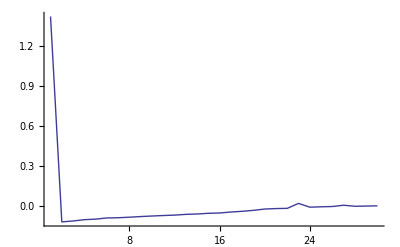

```mathematica
ListPlot[Eigenvalues[m],
Joined->True]
```

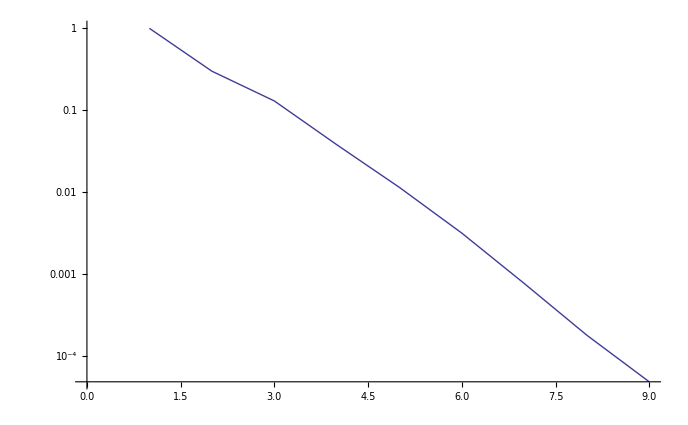

```mathematica
ListLogPlot[Table[PRatio[{3,5},{3,5}, 10^n],{n,0,8}], Joined->True]
```